```mathematica
I1[f_,g_,K_]:=∫_K^∞ g[x]f[x]ⅆx;
```

```mathematica
I2[f_,g_,K_]:=g[K]∫_K^∞ f[x]ⅆx;
```

```mathematica
f[x_]:=PDF[NormalDistribution[0,1],x];
```

```mathematica
ft[x_]:=PDF[StudentTDistribution[0,1,3],x];
```

```mathematica
ftt[x_,ν_]:=PDF[StudentTDistribution[0,1,ν],x];
```

```mathematica
fl[x_,σ_,K_]:=PDF[LogNormalDistribution[Log[K]-σ^2/2,σ],x];
```

```mathematica
Simplify[Mean[LogNormalDistribution[Log[Subscript[X, 0]]-σ^2/2,σ]]]
```

X_0

```mathematica
Simplify[Variance[LogNormalDistribution[Log[Subscript[X, 0]]-σ^2/2,σ]]]
```

(-1+ⅇ^(σ^2)) X_0^2

```mathematica
f[0]
```

1/(√(2 π))

```mathematica
g[x_]:=x;
```

```mathematica
{I1[f,g,K],I2[f,g,K]}
```

{(ⅇ^(-K^2/2))/(√(2 π)),1/2 K Erfc[K/(√2)]}

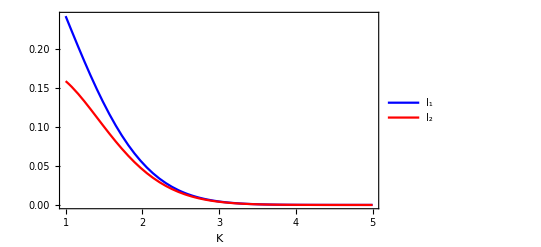

```mathematica
Plot[{(ⅇ^(-K^2/2))/(√(2 π)),1/2 K Erfc[K/(√2)]},{K,1,5},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"I_1","I_2"},FrameLabel->Automatic]
```

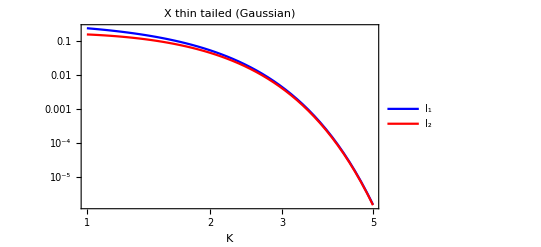

```mathematica
LogLogPlot[{(ⅇ^(-K^2/2))/(√(2 π)),1/2 K Erfc[K/(√2)]},{K,1,5},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"I_1","I_2"},FrameLabel->Automatic,PlotLabel->"X thin tailed (Gaussian)"]
```

```mathematica
{I1[ft,g,K],I2[ft,g,K]}
```

{(3 √3)/(3 π+K^2 π),K (1/2-(√3 K)/((3+K^2) π)-ArcTan[K/(√3)]/π)}

```mathematica
Assuming[x>0&&ν>1&&K>0,{I1[ftt[#,ν]&,g,K],I2[ftt[#,ν]&,g,K]}]
```

{(ν^(ν/2) (K^2+ν)^(1/2-ν/2))/((-1+ν) Beta[ν/2,1/2]),K (1/2-(K Gamma[(1+ν)/2] Hypergeometric2F1[1/2,(1+ν)/2,3/2,-K^2/ν])/(√π √ν Gamma[ν/2]))}

```mathematica
Plot3D[Log[(ν^(ν/2) (K^2+ν)^(1/2-ν/2))/((-1+ν) Beta[ν/2,1/2])]-Log[K (1/2-(K Gamma[(1+ν)/2] Hypergeometric2F1[1/2,(1+ν)/2,3/2,-K^2/ν])/(√π √ν Gamma[ν/2]))],{K,1,5},{ν,1.5,10},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log of Ratio I_1/I_2 for different StudentT[ν]",ImageSize->Large]
```

-Graphics3D-

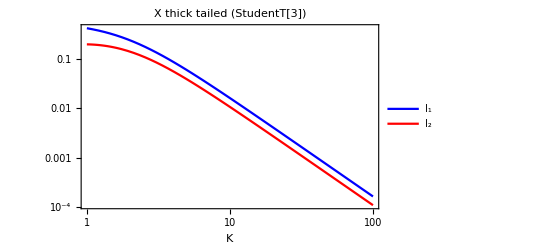

```mathematica
LogLogPlot[{(3 √3)/(3 π+K^2 π),K (1/2-(√3 K)/((3+K^2) π)-ArcTan[K/(√3)]/π)},{K,1,100},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"I_1","I_2"},FrameLabel->Automatic,PlotLabel->"X thick tailed (StudentT[3])"]
```

```mathematica
∫_K^∞ ft[x]ⅆx
```

1/2-(√3 K)/((3+K^2) π)-ArcTan[K/(√3)]/π

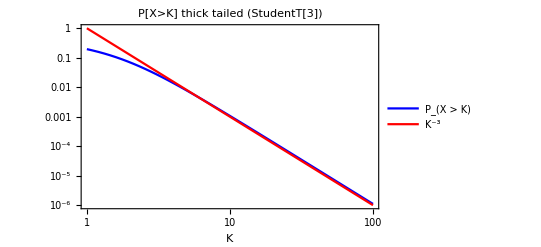

```mathematica
LogLogPlot[{1/2-(√3 K)/((3+K^2) π)-ArcTan[K/(√3)]/π,K^-3},{K,1,100},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"P_(X > K)","K^-3"},FrameLabel->Automatic,PlotLabel->"P[X>K] thick tailed (StudentT[3])"]
```

```mathematica
g1[x_]:=1;
```

```mathematica
{I1[f,g1,K],I2[f,g1,K]}
```

{1/2 Erfc[K/(√2)],1/2 Erfc[K/(√2)]}

```mathematica
Assuming[x>0&&σ>0&&K>0,{I1[fl[#,σ,K]&,g,K],I1[fl[#,σ,K]&,g1,K],∫_K^∞ fl[x,σ,K]ⅆx}]
```

{1/2 K (1+Erf[σ/(2 √2)]),1/2 Erfc[σ/(2 √2)],1/2 Erfc[σ/(2 √2)]}

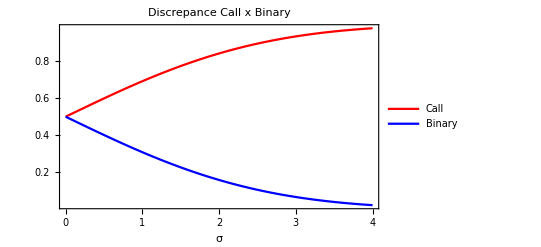

```mathematica
Plot[{1/2 1 (1+Erf[σ/(2 √2)]),1/2 Erfc[σ/(2 √2)]},{σ,0.0001,4},PlotRange->All,Frame->True,PlotStyle->{Red,Blue},PlotLegends->{"Call","Binary"},FrameLabel->Automatic,PlotLabel->"Discrepance Call x Binary"]
```